## Log Log Plot for Density

#### Import single domain

```mathematica
(*Load domain 1 properties file with your local coordinates to generate log-log plot*)
```

```mathematica
domain1 = Import["/Users/lma250/Documents/Research/Manuscripts/2024/Rad21 paper/WingShun Data/Data for processing/domain1 properties.xlsx"][[1]];
```

#### Import domain properties

```mathematica
(*Load data for control cells and rad21 cells to analyze domain properties*)
```

```mathematica
controlEfficiency = Import["/Users/lma250/Documents/Research/Manuscripts/2024/Rad21 paper/WingShun Data/Data for processing/control packing efficiency.xlsx"][[1]];
```

```mathematica
rad21Efficiency = Import["/Users/lma250/Documents/Research/Manuscripts/2024/Rad21 paper/WingShun Data/Data for processing/rad21 packing efficiency.xlsx"][[1]];
```

#### Basic Plot

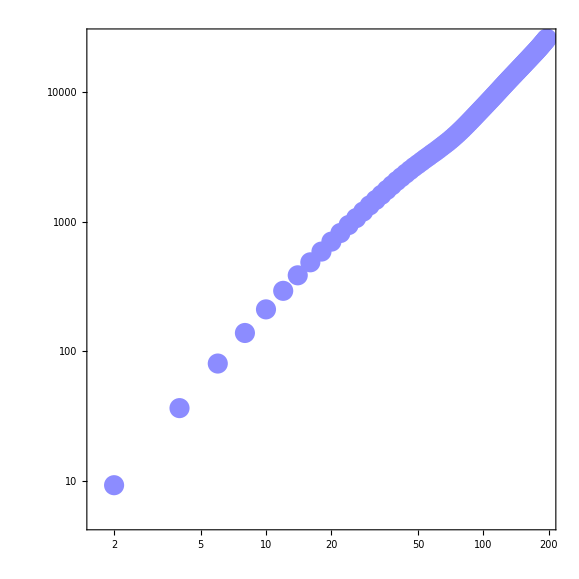

```mathematica
plot =ListLogLogPlot[
Transpose[{Transpose[domain1][[1,2;;]],Transpose[domain1][[2,2;;]]}]
, AspectRatio->1, PlotStyle->Directive[Lighter[Blue,.55], Bold, PointSize[.025]],

AxesStyle->Directive[Black, Bold,22], Frame->{{True, False},{ True,False}},FrameStyle->Directive[Black,Bold,22, Thickness[.0125]], PlotRange->All,
FrameTicks->{
{Table[{10^i,Superscript[10,i]},{i,-10,10}],None},Automatic
}
]
```

#### Calculate Inflection Points

```mathematica
(*Importing the necessary package for smoothing*)
Needs["HypothesisTesting`"]
```

```mathematica
(*Assume data is a list of {x,y} pairs*)
data=Transpose[{Transpose[domain1][[1,2;;]],Transpose[domain1][[2,2;;]]}];
(*Smooth the data*)
windowSize=5;
smoothedData=MovingAverage[data,windowSize];
(*Convert smoothed data to log-log*)
logLogData=Log/@smoothedData;
(*Numerically compute first and second derivatives*)
firstDerivatives=Differences[logLogData[[All,2]]]/Differences[logLogData[[All,1]]];
secondDerivatives=Differences[firstDerivatives];
(*Find where second derivative changes sign*)
inflectionPoints=Flatten[Position[Rest[secondDerivatives]*Most[secondDerivatives],_?Negative]];
(*Corresponding x-values of inflection points*)
xInflectionPoints=logLogData[[inflectionPoints,1]];
Exp[xInflectionPoints]
```

{8.,54.,94.,96.,118.,138.,150.,158.,160.,162.}

```mathematica
(*Inflection points were compared locally to estimates from domain boundaries described within the main text*)
```

#### Plot with Highlighted inflection points

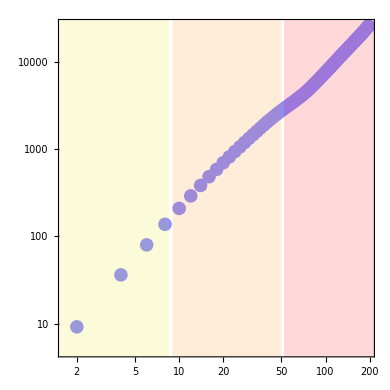

```mathematica
Show[plot,Graphics[{Opacity[0.15],Darker[Yellow,.1],Rectangle[{Log[1],Log[1]},{Log[8.5],Log[50000]}]}],
Graphics[{Opacity[0.15],Orange,Rectangle[{Log[9],Log[1]},{Log[50],Log[50000]}]}],
Graphics[{Opacity[0.15],Red,Rectangle[{Log[52],Log[1]},{Log[250],Log[50000]}]}]
]
```

## All PD Control Data

#### Assign data to control domains

```mathematica
controlDomains = controlEfficiency;
```

#### Histogram plots

```mathematica
controlDomains[[1]]
```

{binarized CVC,Grayscale_density,D,Domain Radius(nm),Packing efficiency}

```mathematica
(*Plot CVC*)
```

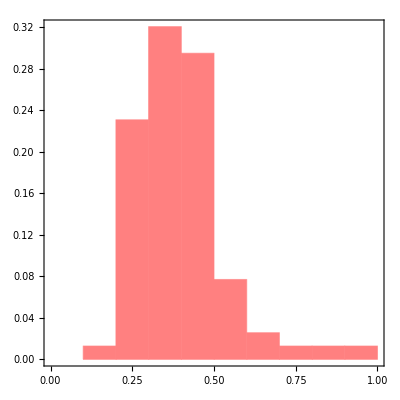

```mathematica
Histogram[Transpose[controlDomains][[1,2;;]],{.1},"Probability",ChartStyle->Lighter[Red,.5],AspectRatio->1,AxesStyle->Directive[Black, Bold,22], Frame->{{True, False},{ True,False}},FrameStyle->Directive[Black,Bold,22, Thickness[.0125]], PlotRange->{{0,1},All} ]
```

```mathematica
(*Plot D*)
```

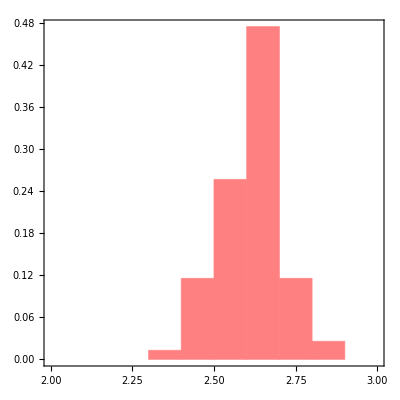

```mathematica
Histogram[Transpose[controlDomains][[3,2;;]],{.1},"Probability",ChartStyle->Lighter[Red,.5],AspectRatio->1,AxesStyle->Directive[Black, Bold,22], Frame->{{True, False},{ True,False}},FrameStyle->Directive[Black,Bold,22, Thickness[.0125]], PlotRange->{{2,3},All} ]
```

```mathematica
(*Plot Radius*)
```

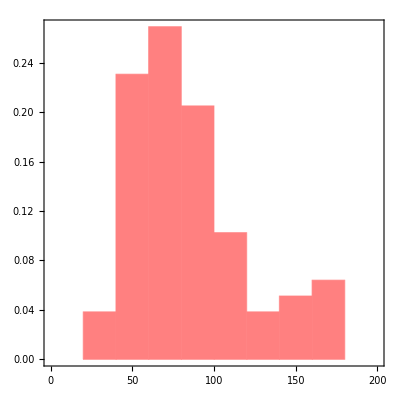

```mathematica
Histogram[Transpose[controlDomains][[4,2;;]],{20},"Probability",ChartStyle->Lighter[Red,.5],AspectRatio->1,AxesStyle->Directive[Black, Bold,22], Frame->{{True, False},{ True,False}},FrameStyle->Directive[Black,Bold,22, Thickness[.0125]], PlotRange->{{0,200},All} ]
```

## Comparison with Rad21 Data

#### Import

```mathematica
rad21Domains = rad21Efficiency;
```

```mathematica
(*Calculate proportion of domains lost with depletion, note that omit first point as it is the index header and not a value*)
```

```mathematica
N[Length[rad21Domains[[2;;]]]/Length[controlDomains[[2;;]]]]
```

0.794872

#### Plots

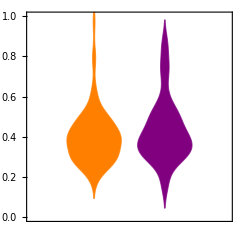

```mathematica
DistributionChart[{Transpose[controlDomains][[1,2;;]],Transpose[rad21Domains][[1,2;;]]}, AspectRatio->1, BarSpacing->Small, ChartStyle->{Orange, Purple}, ChartBaseStyle->EdgeForm[Thick], PlotRangePadding->{{None, None},{None, None}}, Method->{"BoxWidth" -> "Fixed"},Frame->{{True, False},{ True,False}},FrameStyle->Directive[Black,Bold,22, Thickness[.0125]], PlotRange->{All,{0,1}}]
```

```mathematica
(*Statistical testing for domain CVC*)
TTest[{Transpose[rad21Domains][[1,2;;]],Transpose[controlDomains][[1,2;;]]}]
```

TTest::nortst: At least one of the p-values in {0.00021588,0.00180996}, resulting from a test for normality, is below 0.025. The tests in {T} require that the data is normally distributed.

0.197803

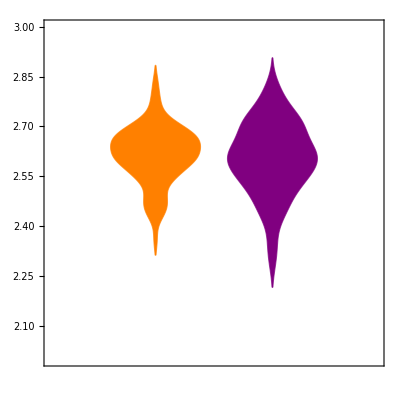

```mathematica
DistributionChart[{Transpose[controlDomains][[3,2;;]],Transpose[rad21Domains][[3,2;;]]}, AspectRatio->1, BarSpacing->Small, ChartStyle->{Orange, Purple}, ChartBaseStyle->EdgeForm[Thick], PlotRangePadding->{{None, None},{None, None}}, Method->{"BoxWidth" -> "Fixed"},Frame->{{True, False},{ True,False}},FrameStyle->Directive[Black,Bold,22, Thickness[.0125]], PlotRange->{All,{2,3}}]
```

```mathematica
(*Statistical testing for domain D*)
TTest[{Transpose[rad21Domains][[1,3;;]],Transpose[controlDomains][[1,3;;]]}]
```

TTest::nortst: At least one of the p-values in {0.000244123,0.00206739}, resulting from a test for normality, is below 0.025. The tests in {T} require that the data is normally distributed.

0.157691

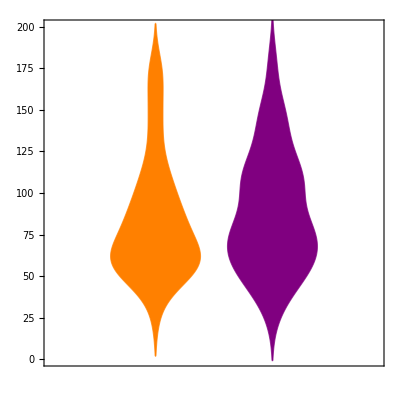

```mathematica
DistributionChart[{Transpose[controlDomains][[4,2;;]],Transpose[rad21Domains][[4,2;;]]}, AspectRatio->1, BarSpacing->Small, ChartStyle->{Orange, Purple}, ChartBaseStyle->EdgeForm[Thick], PlotRangePadding->{{None, None},{None, None}}, Method->{"BoxWidth" -> "Fixed"},Frame->{{True, False},{ True,False}},FrameStyle->Directive[Black,Bold,22, Thickness[.0125]], PlotRange->{All,{0,200}}]
```

```mathematica
(*Statistical testing for domain Radius*)
TTest[{Transpose[rad21Domains][[1,4;;]],Transpose[controlDomains][[1,4;;]]}]
```

TTest::nortst: At least one of the p-values in {0.000111565,0.0193706}, resulting from a test for normality, is below 0.025. The tests in {T} require that the data is normally distributed.

0.113474

#### Quadrant Analysis

```mathematica
controlMassRadius = Transpose[
{Transpose[controlDomains][[c,2;;]],Transpose[controlDomains][[b,2;;]]
}]
```

{{0.63735,60.},{0.816156,50.},{0.389281,128.},{0.386711,146.},{0.393905,82.},{0.535483,66.},{0.51869,80.},{0.413483,112.},{0.442875,80.},{0.356455,148.},{0.282198,154.},{0.435702,84.},{0.329508,176.},{0.406127,70.},{0.971722,22.},{0.499438,72.},{0.369262,166.},{0.570588,60.},{0.376655,114.},{0.313643,96.},{0.419798,70.},{0.410216,168.},{0.387366,104.},{0.492617,102.},{0.479342,50.},{0.563944,60.},{0.347654,112.},{0.47164,104.},{0.5017,60.},{0.476145,90.},{0.485761,50.},{0.487985,68.},{0.309141,92.},{0.445318,84.},{0.429902,86.},{0.424254,98.},{0.474259,56.},{0.766704,58.},{0.354583,170.},{0.399918,94.},{0.460098,64.},{0.615321,48.},{0.351782,84.},{0.36248,70.},{0.298029,126.},{0.303819,178.},{0.390627,98.},{0.380712,144.},{0.295583,74.},{0.420649,74.},{0.320697,68.},{0.208324,58.},{0.416887,64.},{0.506831,56.},{0.250488,52.},{0.295942,70.},{0.347529,82.},{0.349822,114.},{0.311347,104.},{0.40968,60.},{0.249563,86.},{0.358429,46.},{0.299443,56.},{0.268075,86.},{0.298244,78.},{0.474386,54.},{0.40871,54.},{0.30025,50.},{0.285288,58.},{0.261889,56.},{0.236031,60.},{0.29312,38.},{0.272318,44.},{0.236218,130.},{0.392901,62.},{0.25586,60.},{0.253787,34.},{0.178665,56.}}

```mathematica
rad21MassRadius =Transpose[
{Transpose[rad21Domains][[c,2;;]],Transpose[rad21Domains][[b,2;;]]
}]
```

{{0.418423,144.},{0.552592,78.},{0.373582,152.},{0.483867,116.},{0.517909,66.},{0.706852,84.},{0.867487,52.},{0.814087,26.},{0.765998,44.},{0.412496,124.},{0.519973,104.},{0.74592,54.},{0.401731,152.},{0.327258,180.},{0.454125,106.},{0.869381,36.},{0.418329,112.},{0.438515,122.},{0.437491,72.},{0.520451,98.},{0.380597,78.},{0.475283,94.},{0.364396,112.},{0.71375,56.},{0.529764,60.},{0.6101,74.},{0.367106,174.},{0.335228,140.},{0.315647,108.},{0.289504,108.},{0.398741,94.},{0.401064,68.},{0.3849,144.},{0.312453,102.},{0.334561,54.},{0.598017,38.},{0.271662,84.},{0.476422,42.},{0.4781,46.},{0.424299,104.},{0.378297,128.},{0.515184,80.},{0.367168,74.},{0.247463,78.},{0.379112,146.},{0.523718,76.},{0.387392,130.},{0.49828,52.},{0.304958,106.},{0.340281,70.},{0.335389,62.},{0.308837,110.},{0.340842,56.},{0.286789,60.},{0.317336,114.},{0.1553,70.},{0.294895,66.},{0.329408,80.},{0.286768,80.},{0.322646,66.},{0.190463,52.},{0.163261,60.}}

#### Separate into Groups

```mathematica
nascent={Select[controlMassRadius,(#[[1]]<intersect3[[1]]&&#[[2]]<intersect3[[2]])&],
Select[rad21MassRadius,(#[[1]]<intersect3[[1]]&&#[[2]]<intersect3[[2]])&]};
decaying={Select[controlMassRadius,(#[[1]]<intersect3[[1]]&&#[[2]]>intersect3[[2]])&],
Select[rad21MassRadius,(#[[1]]<intersect3[[1]]&&#[[2]]>intersect3[[2]])&]};
mature={Select[controlMassRadius,(#[[1]]>intersect3[[1]])&],
Select[rad21MassRadius,(#[[1]]>intersect3[[1]]&)]};
```

```mathematica
Length[#]&/@mature
Length[#]&/@decaying
Length[#]&/@nascent
```

{29,27}

{22,18}

{27,17}

```mathematica
1-N[27/29]
1-N[18/22]
1-N[17/27]
```

0.0689655

0.181818

0.37037

```mathematica
nascentUseControl={Select[controlMassRadius,(#[[1]]<intersect4[[1]]&&#[[2]]<intersect4[[2]])&],
Select[rad21MassRadius,(#[[1]]<intersect4[[1]]&&#[[2]]<intersect4[[2]])&]};
decayingUseControl={Select[controlMassRadius,(#[[1]]<intersect4[[1]]&&#[[2]]>intersect4[[2]])&],
Select[rad21MassRadius,(#[[1]]<intersect4[[1]]&&#[[2]]>intersect4[[2]])&]};
matureUseControl={Select[controlMassRadius,(#[[1]]>intersect4[[1]])&],
Select[rad21MassRadius,(#[[1]]>intersect4[[1]]&)]};
```

```mathematica
Length[#]&/@matureUseControl
Length[#]&/@decayingUseControl
Length[#]&/@nascentUseControl
```

{35,30}

{22,17}

{21,15}

```mathematica
N[1-(30/35)]
N[1-(17/22)]
N[1-(15/21)]
```

0.142857

0.227273

0.285714

## Packing Efficiency Plots

#### Efficiency vs Area

```mathematica
(*Index for each feature. Note that gray-scale intensity and binarized CVC are two methods for estimating DNA per unit area. Analysis with binarized CVC was utilized for this manuscript in line with the method described by Ou et al, Li et al, and Agrawal et al*)
```

```mathematica
(*Indices for mapping*)
rad21Efficiency[[1]]
```

{binarized CVC,Grayscale_density,D,Domain Radius(nm),Packing Efficiency}

```mathematica
(*Plot packing efficiency vs domain size*)
```

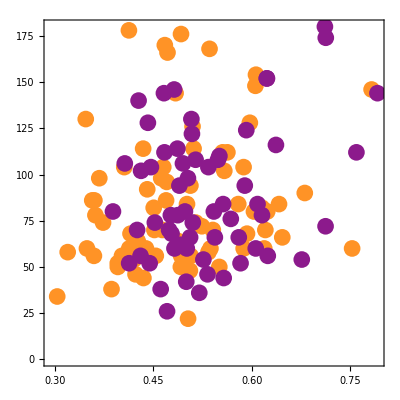

```mathematica
a=5;
b=4;
plot3=ListPlot[
{Transpose[
{Transpose[controlEfficiency][[a,2;;]],Transpose[controlEfficiency][[b,2;;]]
}],
Transpose[
{Transpose[rad21Efficiency][[a,2;;]],Transpose[rad21Efficiency][[b,2;;]]
}]}
, AspectRatio->1, PlotRange->{All,All}, 
PlotStyle->{Directive[PointSize[.03],Lighter[Orange, .15]], Directive[PointSize[.03],Lighter[Purple,.1]]}, Frame->{{True, False},{ True,False}},FrameStyle->Directive[Black,Bold,22, Thickness[.0125]], PlotRange->All, AxesStyle->Directive[Black, Bold, 24]
]
```

#### Averages for transition points

```mathematica
intersectControl ={Mean[Flatten[{Transpose[controlEfficiency][[a,2;;]]}]],
Mean[Flatten[{Transpose[controlEfficiency][[b,2;;]]}]]}
```

{0.490868,83.8205}

#### Plot with means indicated

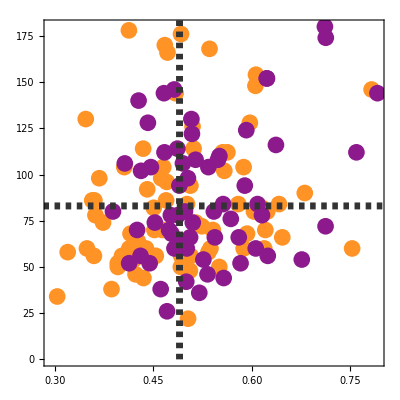

```mathematica
Show[plot3,
Graphics[{Dashing[.01,.1],Lighter[Black,.2], AbsoluteThickness[5],Line[{{0,83},{2,83}}]}],
Graphics[{Dashing[.01,.1],Lighter[Black,.2], AbsoluteThickness[5],Line[{{.49,0},{.49,200}}]}]
]
```

#### Quadrant Analysis

```mathematica
controlEfficientRadius = Transpose[
{Transpose[controlEfficiency][[a,2;;]],Transpose[controlEfficiency][[b,2;;]]
}]
```

{{0.753386,60.},{0.550691,50.},{0.597289,128.},{0.783115,146.},{0.61575,82.},{0.646796,66.},{0.603558,80.},{0.555756,112.},{0.623847,80.},{0.605827,148.},{0.606667,154.},{0.579623,84.},{0.492261,176.},{0.620976,70.},{0.503027,22.},{0.524092,72.},{0.471644,166.},{0.619255,60.},{0.511455,114.},{0.470389,96.},{0.451662,70.},{0.535774,168.},{0.587769,104.},{0.558309,102.},{0.49957,50.},{0.587879,60.},{0.563038,112.},{0.465167,104.},{0.537157,60.},{0.681128,90.},{0.492025,50.},{0.59295,68.},{0.440699,92.},{0.641816,84.},{0.46947,86.},{0.367537,98.},{0.402172,56.},{0.435881,58.},{0.467552,170.},{0.506576,94.},{0.488119,64.},{0.50579,48.},{0.501417,84.},{0.463685,70.},{0.509852,126.},{0.412747,178.},{0.462024,98.},{0.483955,144.},{0.373264,74.},{0.514667,74.},{0.415182,68.},{0.534121,58.},{0.426177,64.},{0.453765,56.},{0.395762,52.},{0.540764,70.},{0.45057,82.},{0.434466,114.},{0.405667,104.},{0.438753,60.},{0.356792,86.},{0.422845,46.},{0.492483,56.},{0.360051,86.},{0.361625,78.},{0.406602,54.},{0.42033,54.},{0.39584,50.},{0.319312,58.},{0.506937,56.},{0.348702,60.},{0.386196,38.},{0.434907,44.},{0.346886,130.},{0.421966,62.},{0.413323,60.},{0.303327,34.},{0.359332,56.}}

```mathematica
rad21EfficientRadius =Transpose[
{Transpose[rad21Efficiency][[a,2;;]],Transpose[rad21Efficiency][[b,2;;]]
}]
```

{{0.792061,144.},{0.615817,78.},{0.623385,152.},{0.637123,116.},{0.580395,66.},{0.609039,84.},{0.583126,52.},{0.470944,26.},{0.557393,44.},{0.591866,124.},{0.534029,104.},{0.67656,54.},{0.623154,152.},{0.711841,180.},{0.495202,106.},{0.52014,36.},{0.759937,112.},{0.508931,122.},{0.712852,72.},{0.502811,98.},{0.476763,78.},{0.489762,94.},{0.467039,112.},{0.62466,56.},{0.606324,60.},{0.452337,74.},{0.713182,174.},{0.427507,140.},{0.514527,108.},{0.548685,108.},{0.589563,94.},{0.477793,68.},{0.466189,144.},{0.43132,102.},{0.526373,54.},{0.461231,38.},{0.556511,84.},{0.500264,42.},{0.532715,46.},{0.446307,104.},{0.441699,128.},{0.542388,80.},{0.510227,74.},{0.487352,78.},{0.48176,146.},{0.568243,76.},{0.508087,130.},{0.444411,52.},{0.406461,106.},{0.474057,70.},{0.491165,62.},{0.550829,110.},{0.430509,56.},{0.482257,60.},{0.486757,114.},{0.425265,70.},{0.54389,66.},{0.388399,80.},{0.498238,80.},{0.506132,66.},{0.413117,52.},{0.501039,60.}}

#### Separate into Groups

```mathematica
(*Partition into groups based on their size and packing efficiency to calculate their distributions*)
```

```mathematica
nascentEfficient={Select[controlEfficientRadius,(#[[1]]<intersectControl[[1]]&&#[[2]]<intersectControl[[2]])&],
Select[rad21EfficientRadius,(#[[1]]<intersectControl[[1]]&&#[[2]]<intersectControl[[2]])&]};
decayingEfficient={Select[controlEfficientRadius,(#[[1]]<intersectControl[[1]]&&#[[2]]>intersectControl[[2]])&],
Select[rad21EfficientRadius,(#[[1]]<intersectControl[[1]]&&#[[2]]>intersectControl[[2]])&]};
matureEfficient={Select[controlEfficientRadius,(#[[1]]>intersectControl[[1]])&],
Select[rad21EfficientRadius,(#[[1]]>intersectControl[[1]]&)]};
```

```mathematica
(Length[#]&/@matureEfficient)
(Length[#]&/@decayingEfficient)
(Length[#]&/@nascentEfficient)
```

{38,39}

{15,10}

{25,13}

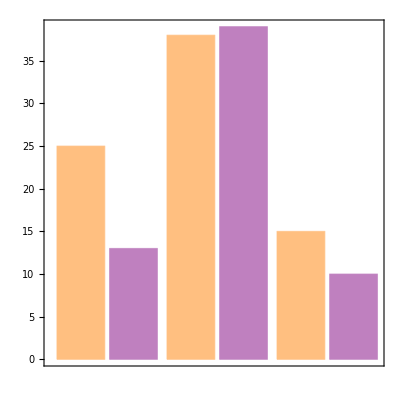

```mathematica
BarChart[{(Length[#]&/@nascentEfficient),
(Length[#]&/@matureEfficient),
(Length[#]&/@decayingEfficient)
},AspectRatio->1, BarSpacing->Small, ChartStyle->{Lighter[Orange, .5],Lighter[Purple,.5]}, ChartBaseStyle->EdgeForm[Thick], PlotRangePadding->{{None, None},{None, None}}, Method->{"BoxWidth" -> "Fixed"},Frame->{{True, False},{ True,False}},FrameStyle->Directive[Black,Bold,22, Thickness[.0125]]]
```

## Micro-C Data Analysis

#### Load Data

```mathematica
basepairCalc = Import["/Users/lma250/Documents/Research/Manuscripts/2024/Rad21 paper/WingShun Data/Data for processing/RAD21_DomainSizeInKbps.xlsx","Data"][[1]];
```

```mathematica
controlLoops = Import["/Users/lma250/Documents/Research/Manuscripts/2024/Rad21 paper/Public AID2 Data/Control/loops/controlloops.xlsx","Data"][[1]];
controlDomains = Import["/Users/lma250/Documents/Research/Manuscripts/2024/Rad21 paper/Public AID2 Data/Control/domains/controldomains.xlsx","Data"][[1]];
rad21Loops = Import["/Users/lma250/Documents/Research/Manuscripts/2024/Rad21 paper/Public AID2 Data/AID Treated/loops/rad21loops.xlsx","Data"][[1]];
rad21Domains = Import["/Users/lma250/Documents/Research/Manuscripts/2024/Rad21 paper/Public AID2 Data/AID Treated/domains/rad21domains.xlsx","Data"][[1]];
```

#### Format Data into same chromosomes

```mathematica
rad21LoopsSelf = Select[rad21Loops,#[[1]]==#[[4]]&];
rad21DomainsSelf = Select[rad21Domains,#[[1]]==#[[4]]&];

controlLoopsSelf = Select[controlLoops,#[[1]]==#[[4]]&];
controlDomainsSelf = Select[controlDomains,#[[1]]==#[[4]]&];
```

#### Compare RAD21 to Control

```mathematica
N[Length[rad21DomainsSelf]/Length[controlDomainsSelf]]
N[Length[rad21LoopsSelf]/Length[controlLoopsSelf]]
```

0.0292304

0.0576703

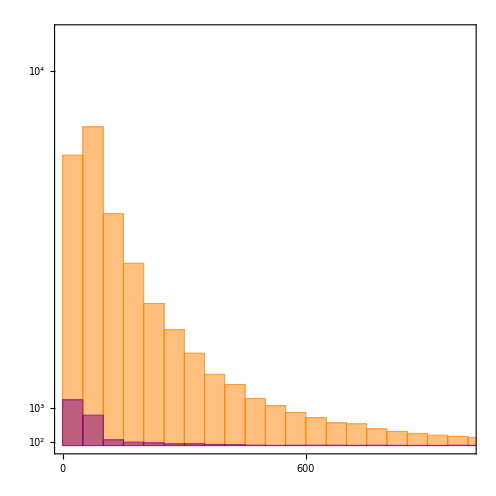

```mathematica
Histogram[{(Transpose[controlLoopsSelf][[6]]-Transpose[controlLoopsSelf][[2]]),
(Transpose[rad21LoopsSelf][[6]]-Transpose[rad21LoopsSelf][[3]])
}, PlotRange->{{0,1*10^6},{0,1.1*10^4}},ChartStyle->{Orange,Purple, Lighter[Blue,.25]},
 AspectRatio->1, PlotRangePadding->{{None, None},{None, None}}, Method->{"BoxWidth" -> "Fixed"},Frame->{{True, False},{ True,False}},FrameStyle->Directive[Black,Bold,22, Thickness[.0125]],FrameTicks->{
{Table[{10^i,Superscript[10,i]},{i,2,4}],None},{Table[{i*10^5,100*i},{i,0,21,3}],None}
}]
```

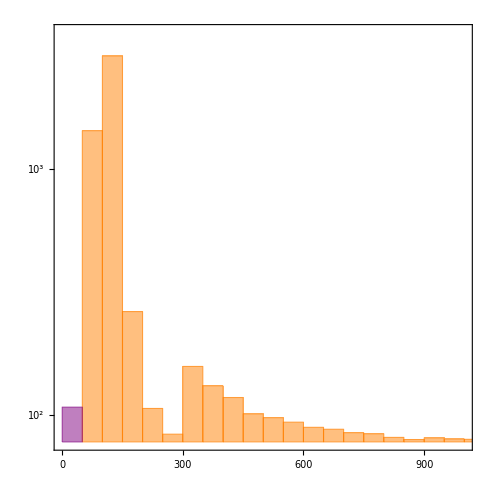

```mathematica
Histogram[{(Transpose[controlDomainsSelf][[3]]-Transpose[controlDomainsSelf][[2]]),
(Transpose[rad21DomainsSelf][[6]]-Transpose[rad21DomainsSelf][[3]])
},PlotRange->{{0,1*10^6},{0,1.5*10^3}},ChartStyle->{Orange,Purple, Lighter[Blue,.25]},
 AspectRatio->1, PlotRangePadding->{{None, None},{None, None}}, Method->{"BoxWidth" -> "Fixed"},Frame->{{True, False},{ True,False}},FrameStyle->Directive[Black,Bold,22, Thickness[.0125]],FrameTicks->{
{Table[{10^i,Superscript[10,i]},{i,2,4}],None},{Table[{i*10^5,100*i},{i,0,12,3}],None}
}]
```

#### Compare PDs to TADS and Loops

```mathematica
(*PD data is available in basepairCalc with first object being the control values*)
```

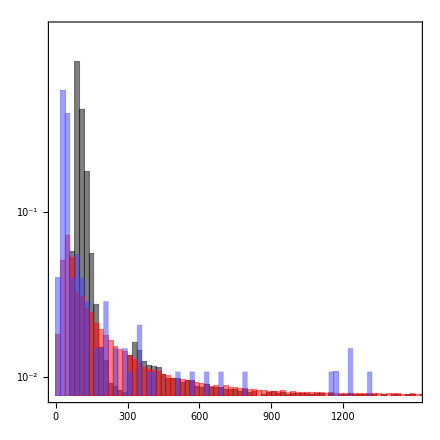

```mathematica
Histogram[
{(Transpose[controlDomainsSelf][[3]]-Transpose[controlDomainsSelf][[2]])/1000,
(Transpose[controlLoopsSelf][[6]]-Transpose[controlLoopsSelf][[2]])/1000,
Transpose[basepairCalc][[1,2;;]]}
,{20},"Probability",
ChartStyle->{Black,Red, Lighter[Blue,.25], Orange},
 AspectRatio->1, PlotRange->{{0,1500},{0,2*1*10^(-1)}},PlotRangePadding->{{None, None},{None, None}}, Method->{"BoxWidth" -> "Fixed"},Frame->{{True, False},{ True,False}},FrameStyle->Directive[Black,Bold,24, Thickness[.0125]],FrameTicks->{
{Table[{10^i,Superscript[10,i]},{i,-2,0}],None},{Table[{i*10^2,100*i},{i,0,12,3}],None}
}]
```

#### Size Values

```mathematica
Mean[(Transpose[controlLoopsSelf][[6]]-Transpose[controlLoopsSelf][[2]])/1000]
Quartiles[(Transpose[controlLoopsSelf][[6]]-Transpose[controlLoopsSelf][[2]])/1000]
Max[(Transpose[controlLoopsSelf][[6]]-Transpose[controlLoopsSelf][[2]])/1000]
Min[(Transpose[controlLoopsSelf][[6]]-Transpose[controlLoopsSelf][[2]])/1000]
```

331.857

{72.,170.,365.}

9060.

9.

```mathematica
Mean[(Transpose[controlDomainsSelf][[3]]-Transpose[controlDomainsSelf][[2]])/1000]
Quartiles[(Transpose[controlDomainsSelf][[3]]-Transpose[controlDomainsSelf][[2]])/1000]
Max[(Transpose[controlDomainsSelf][[3]]-Transpose[controlDomainsSelf][[2]])/1000]
Min[(Transpose[controlDomainsSelf][[3]]-Transpose[controlDomainsSelf][[2]])/1000]
```

226.573

{95.,130.,320.}

2550.

60.

```mathematica
Mean[Transpose[basepairCalc][[1,2;;]]]
Quartiles[Transpose[basepairCalc][[1,2;;]]]
Max[Transpose[basepairCalc][[1,2;;]]]
Min[Transpose[basepairCalc][[1,2;;]]]
```

218.791

{44.0853,89.3209,252.171}

1306.4

6.27387

## ATAC-Seq Data

#### Functions

```mathematica
sizeSlope[lst_]:=Transpose[{Transpose[lst][[7]],Transpose[lst][[4]]-Transpose[lst][[3]]}]
```

```mathematica
tadQuads[lst_,thrs_]:={Select[sizeSlope[lst],(#[[1]]<=thrs[[1]]&&#[[2]]<=thrs[[2]])&],
Select[sizeSlope[lst],(#[[1]]<=thrs[[1]]&&#[[2]]>thrs[[2]])&],
Select[sizeSlope[lst],(#[[1]]>thrs[[1]]&&#[[2]]<thrs[[2]])&],
Select[sizeSlope[lst],(#[[1]]>thrs[[1]]&&#[[2]]>thrs[[2]])&]}
```

```mathematica
chrList =Flatten[Append[Table[StringJoin["chr",ToString[i]],{i,1,22}],{"chrX","chrY"}]];
syntaxMapNumericChr = Table[chrList[[i]]->i,{i,22}];
syntaxMapNumericChrXY = Table[chrList[[i]]->i,{i,24}];
```

```mathematica
orgCondByChromosome[marker_]:=SplitBy[SortBy[Select[marker,(StringLength[#[[1]]]<=5&&#[[9]]>1)&]/.syntaxMapNumericChrXY,1],#[[1]]&];
```

```mathematica
orgLoopsByChromosome[marker_]:=SplitBy[SortBy[marker/.syntaxMapNumericChrXY,1],#[[1]]&];
```

```mathematica
loopStartStop[lst_]:=Table[{
lst[[i,1]],
Mean[{lst[[i,2]],lst[[i,3]]}],
Mean[{lst[[i,5]],lst[[i,6]]}]},{i,Length[lst]}];
```

```mathematica
tadStartStop[lst_]:=Table[{
lst[[i,1]],lst[[i,2]],lst[[i,3]]},{i,Length[lst]}];
```

#### Organize HiC by Chromosome

```mathematica
controlLoopsByChr = orgLoopsByChromosome[controlLoopsSelf];
controlDomainsByChr = orgLoopsByChromosome[controlDomainsSelf];
rad21LoopsByChr = orgLoopsByChromosome[rad21LoopsSelf];
rad21DomainsByChr = orgLoopsByChromosome[rad21DomainsSelf];
```

#### Load Atac-Seq Data

```mathematica
atacPeaksControl = Import["/Users/lma250/Documents/Research/Manuscripts/2024/Rad21 paper/Public AID2 Data/Control/atac/ENCFF107INQ.bed","Data"];
atacPeaksRad21 = Import["/Users/lma250/Documents/Research/Manuscripts/2024/Rad21 paper/Public AID2 Data/AID Treated/atac/ENCFF460JUY.bed","Data"];
```

```mathematica
atacOrgControl = orgCondByChromosome[atacPeaksControl];
atacOrgRad21= orgCondByChromosome[atacPeaksRad21];
```

#### Global Accessibility

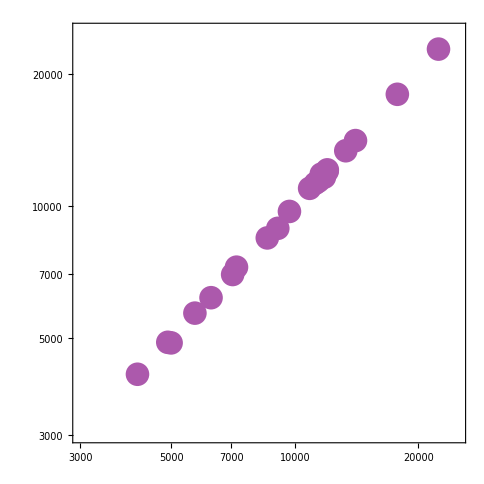

```mathematica
ListLogLogPlot[Table[{Length[atacOrgControl[[i]]],Length[atacOrgRad21[[i]]]},{i,Length[atacOrgControl]-1}], 
PlotStyle->{
Directive[PointSize[.035],Lighter[Purple, .35]]}
, Frame->{{True, False},{ True,False}},FrameStyle->Directive[Black,Bold,22, Thickness[.015]], PlotRange->{{3000,25000},{3000,25000}}, AxesStyle->Directive[Black, Bold, 24], AspectRatio->1,FrameTicks->{
{Table[{i*10^4,10*i},{i,.5,3,1}],None},{Table[{i*10^4,10*i},{i,.5,3,1}],None}
}]
```

#### Map Average Atac positions by chromosome

```mathematica
meanPosAtacControlByChr = Table[N[Mean[#]]&/@Transpose[{Transpose[atacOrgControl[[i]]][[2]],Transpose[atacOrgControl[[i]]][[3]]}],{i,Length[atacOrgControl]}];
meanPosAtacRad21ByChr = Table[N[Mean[#]]&/@Transpose[{Transpose[atacOrgRad21[[i]]][[2]],Transpose[atacOrgRad21[[i]]][[3]]}],{i,Length[atacOrgRad21]}];
```

#### Map TAD and Loop Coordinates by Chromosome

```mathematica
loopControlChrCoord=Table[loopStartStop[controlLoopsByChr[[i]]],{i,Length[controlLoopsByChr]}];
loopRad21ChrCoord=Table[loopStartStop[rad21LoopsByChr[[i]]],{i,Length[rad21LoopsByChr]}];
```

```mathematica
tadControlChrCoord=Table[tadStartStop[controlDomainsByChr[[i]]],{i,Length[controlDomainsByChr]}];
tadRad21ChrCoord=Table[tadStartStop[rad21DomainsByChr[[i]]],{i,Length[rad21DomainsByChr]}];
```

#### Evaluate Peaks within TADs

```mathematica
testAllControlTads = Table[
Select[meanPosAtacControlByChr[[i]],Between[#]]&/@Transpose[{Transpose[tadControlChrCoord[[i]]][[2]],Transpose[tadControlChrCoord[[i]]][[3]]}],{i,Length[tadControlChrCoord]}];
testAllRad21Tads = Table[
Select[meanPosAtacRad21ByChr[[i]],Between[#]]&/@Transpose[{Transpose[tadControlChrCoord[[i]]][[2]],Transpose[tadControlChrCoord[[i]]][[3]]}],{i,Length[tadControlChrCoord]}];
```

```mathematica
testAllControlLoops = Table[
Select[meanPosAtacControlByChr[[i]],Between[#]]&/@Transpose[{Transpose[loopControlChrCoord[[i]]][[2]],Transpose[loopControlChrCoord[[i]]][[3]]}],{i,Length[loopControlChrCoord]}];
testAllRad21Loops = Table[
Select[meanPosAtacRad21ByChr[[i]],Between[#]]&/@Transpose[{Transpose[loopControlChrCoord[[i]]][[2]],Transpose[loopControlChrCoord[[i]]][[3]]}],{i,Length[loopControlChrCoord]}];
```

```mathematica
deltaPeaksTads=Table[(Length[#]&/@testAllControlTads[[i]])-(Length[#]&/@testAllRad21Tads[[i]]),{i,Length[testAllRad21Tads]}];
```

```mathematica
deltaPeaksLoops=Table[(Length[#]&/@testAllControlLoops[[i]])-(Length[#]&/@testAllRad21Loops[[i]]),{i,Length[testAllRad21Loops]}];
```

```mathematica
N[Quartiles[Flatten[deltaPeaksTads]]]
N[Quartiles[Flatten[deltaPeaksLoops]]]
```

{-2.,0.,2.}

{-2.,0.,2.}

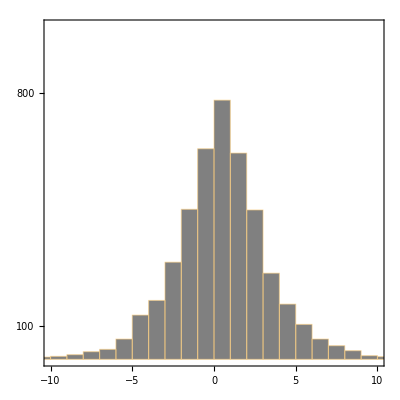

```mathematica
Histogram[Flatten[deltaPeaksTads],ChartStyle->{Gray},
 AspectRatio->1, PlotRange->{{-10,10},{0,1*1*10^(3)}},PlotRangePadding->{{None, None},{None, None}}, Method->{"BoxWidth" -> "Fixed"},Frame->{{True, False},{ True,False}},FrameStyle->Directive[Black,Bold,24, Thickness[.0125]],FrameTicks->{
{Table[{i*100,i*100},{i,1,10,7}],None},Automatic}]
```

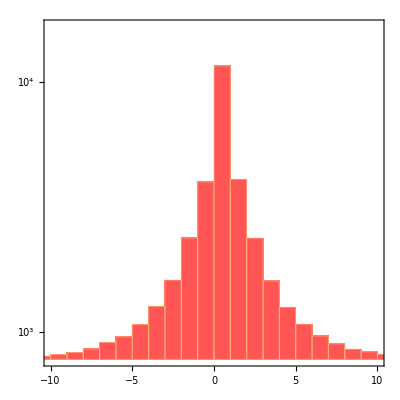

```mathematica
Histogram[Flatten[deltaPeaksLoops], AspectRatio->1, PlotRange->{{-10,10},{0,1.2*1*10^(4)}},ChartStyle->{Lighter[Red]},PlotRangePadding->{{None, None},{None, None}}, Method->{"BoxWidth" -> "Fixed"},Frame->{{True, False},{ True,False}},FrameStyle->Directive[Black,Bold,24, Thickness[.0125]],FrameTicks->{
{Table[{10^i,Superscript[10,i]},{i,3,4}],None},Automatic}]
```